src: "Introducing Mathematica, Stephen Wolfram"

Stephen Wolfram, 1989 (56:58):

“Of course the only way you’ll really learn about a computer system like Mathematica is by actually using it.
I hope you’ll enjoy using Mathematica.”

## Part 1

### Numerical Calculation

```mathematica
3+5
```

8

```mathematica
3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

Let’s check how many digits the number has:

```mathematica
IntegerLength@%5
```

478

Some other ways to get the same result:

```mathematica
StringLength@ToString@
```

478

```mathematica
DigitCount@
```

{44,47,39,48,47,53,41,63,39,57}

```mathematica
Total@{44,47,39,48,47,53,41,63,39,57}
```

478

```mathematica
Plus@@{44,47,39,48,47,53,41,63,39,57}
```

478

### Symbolic and Algebraic Calculation

```mathematica
(12 + x + x^2)^6
```

(12+x+x^2)^6

```mathematica
Expand@
```

2985984+1492992 x+1804032 x^2+656640 x^3+416880 x^4+112392 x^5+47881 x^6+9366 x^7+2895 x^8+380 x^9+87 x^10+6 x^11+x^12

```mathematica
Factor@
```

(12+x+x^2)^6

```mathematica
Integrate[x/(x^3-1),x]
```

ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

### Graphics

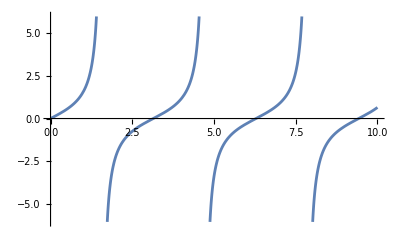

```mathematica
Plot[Tan[x],{x,0,10}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

Here I tried to recreate the “Copy & Paste” code at 5:20 minute:

```mathematica
Plot3D[(Sin[x] Cos[y]),
{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Manipulate[
Plot3D[(Sin[x+n] Cos[y+n]),
{x,-Pi,Pi},{y,-Pi,Pi}],
{n,0,Pi-Pi/10,Pi/10}]
```

```mathematica
Manipulate[
Plot3D[(Sin[x+n] Cos[y+n]),
{x,-Pi,Pi},{y,-Pi,Pi},ColorFunction->Function[{x,y,z},Hue[z]]],
{n,0,Pi-Pi/10,Pi/10}]
```

```mathematica
RGBColor[(1+Sin[x] Cos[y])/2,1,1]
```

```mathematica
Manipulate[
Plot3D[(Sin[x+n] Cos[y+n]),
{x,-Pi,Pi},{y,-Pi,Pi},
ColorFunction->Function[{x,y,z},RGBColor[(1+Sin[x] Cos[y])/2,1,1]]],
{n,0,Pi-Pi/10,Pi/10}]
```

```mathematica
Animate[
Plot3D[(Sin[x+n] Cos[y+n]),
{x,-Pi,Pi},{y,-Pi,Pi},
ColorFunction->Function[{x,y},Hue[(1+Sin[x] Cos[y])/2,1,1]]],
{n,0,Pi-Pi/10,Pi/10}]
```

## Part 2

### Numerical Calculation

```mathematica
43+78
```

121

```mathematica
4/8+1/7
```

9/14

```mathematica
3^200
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044001

```mathematica
N@
```

2.65614×10^95

```mathematica
N[Sqrt[19],200]
```

4.3588989435406735522369819838596156591370039252324449368903441381595573282031580856561591558519445269056586212982742136295839927838261170121565608364174699009777529188794058900619967156631207402231024

```mathematica
^2
```

19.

```mathematica
-19
```

0.

```mathematica
(3+5 I)^10
```

-28984576-34989600 ⅈ

```mathematica
Log[-2.3]
```

0.832909+3.14159 ⅈ

```mathematica
BesselJ[2.5,5+6 I]
```

23.2024-35.7887 ⅈ

```mathematica
Hypergeometric2F1[3.4,5.6,4+I,4.6+2 I]
```

0.00461369+0.00196591 ⅈ

```mathematica
FactorInteger[23412341]
```

{{73,1},{137,1},{2341,1}}

Let’s check that result:

```mathematica
(First@#)^(#[[2]])&/@{{73,1},{137,1},{2341,1}}
```

{73,137,2341}

```mathematica
Times@@{73,137,2341}
```

23412341

Looks good :)

It’s probably easier to use the built-in function “Power” for this kind of calculation.

```mathematica
Power@@@{{73,1},{137,1},{2341,1}}
```

{73,137,2341}

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
FactorInteger@
```

{{2,97},{3,48},{5,24},{7,16},{11,9},{13,7},{17,5},{19,5},{23,4},{29,3},{31,3},{37,2},{41,2},{43,2},{47,2},{53,1},{59,1},{61,1},{67,1},{71,1},{73,1},{79,1},{83,1},{89,1},{97,1}}

Let’s write a function that does this kind of check:

```mathematica
fGetNumberFromIntergerFactors[factors_]:=Module[{primePowers,resultingNumber},
(* Get the powers of the primes. *)
primePowers=Power@@@factors;
(* Calculate the number from the prime factors. *)
resultingNumber=Times@@primePowers;

Return[resultingNumber];
]

number1=123!
factors=FactorInteger@number1

number1==fGetNumberFromIntergerFactors[factors]
```

12146304367025329675766243241881295855454217088483382315328918161829235892362167668831156960612640202170735835221294047782591091570411651472186029519906261646730733907419814952960000000000000000000000000000

{{2,117},{3,59},{5,28},{7,19},{11,12},{13,9},{17,7},{19,6},{23,5},{29,4},{31,3},{37,3},{41,3},{43,2},{47,2},{53,2},{59,2},{61,2},{67,1},{71,1},{73,1},{79,1},{83,1},{89,1},{97,1},{101,1},{103,1},{107,1},{109,1},{113,1}}

True

```mathematica
A={{3,4},{-2,7}};
invA=Inverse@A;
eigVal=Eigenvalues@invA;

MatrixForm/@{A,invA,eigVal}
```

{(3 | 4
-2 | 7),(7/29 | -4/29
2/29 | 3/29),(5/29+(2 ⅈ)/29
5/29-(2 ⅈ)/29)}

```mathematica
(kindaHilbertMatrix=Table[1/(i+j+1),{i,4},{j,4}])//MatrixForm
```

(1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7
1/5 | 1/6 | 1/7 | 1/8
1/6 | 1/7 | 1/8 | 1/9)

```mathematica
invB=Inverse@kindaHilbertMatrix
Det@invB
```

{{1200,-6300,10080,-5040},{-6300,35280,-58800,30240},{10080,-58800,100800,-52920},{-5040,30240,-52920,28224}}

10668672000

```mathematica
Eigenvalues[N@invB]
```

{163949.,1521.33,32.3242,1.32327}

### Symbolic and Algebraic Calculation

```mathematica
x+x
```

2 x

```mathematica
(x+1)(x+3)
```

(1+x) (3+x)

```mathematica
Expand@
```

3+4 x+x^2

```mathematica
Factor@
```

(1+x) (3+x)

```mathematica
Factor[x^16-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8)

```mathematica
Expand@
```

-1+x^16

```mathematica
Solve[x^2+2 a x + 1 ==0,x]
```

{{x→-a-√(-1+a^2)},{x→-a+√(-1+a^2)}}

```mathematica
Solve[x^5+3x+1==0,x]
```

{{x→},{x→},{x→},{x→},{x→}}

```mathematica
N@
```

{{x→-0.331989},{x→-0.839072-0.943852 ⅈ},{x→-0.839072+0.943852 ⅈ},{x→1.00507-0.937259 ⅈ},{x→1.00507+0.937259 ⅈ}}

Let’s plot the roots:

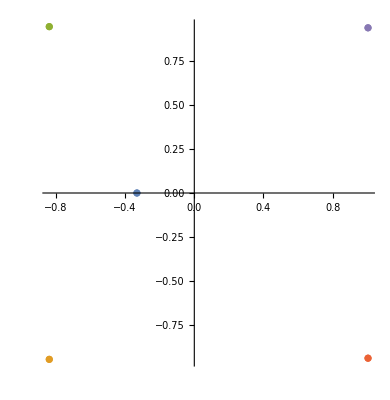

```mathematica
ComplexListPlot[Values@]
```

It looks like there is only one real root, let’s check that:

```mathematica
roots=Flatten@Values@
```

{,,,,}

```mathematica
RealValuedNumericQ/@roots
```

{True,False,False,False,False}

```mathematica
Solve[{x^2+y^2==1,x^3+x y +y^2==0},{x,y}]
```

{{x→,y→ (-2++2 ^2-2 ^3+^4)},{x→,y→ (-2++2 ^2-2 ^3+^4)},{x→,y→ (-2++2 ^2-2 ^3+^4)},{x→,y→ (-2++2 ^2-2 ^3+^4)},{x→,y→ (-2++2 ^2-2 ^3+^4)},{x→,y→ (-2++2 ^2-2 ^3+^4)}}

```mathematica
N@
```

{{x→-0.872669,y→-0.488312},{x→-0.578447,y→0.81572},{x→0.756535-0.33851 ⅈ,y→-0.802541-0.319105 ⅈ},{x→0.756535+0.33851 ⅈ,y→-0.802541+0.319105 ⅈ},{x→0.969023-1.39457 ⅈ,y→1.63884+0.824594 ⅈ},{x→0.969023+1.39457 ⅈ,y→1.63884-0.824594 ⅈ}}

```mathematica
Solve[a x+b==0,x]
```

{{x→-b/a}}

```mathematica
Reduce[a x+b==0,x]
```

(b==0&&a==0)||(a≠0&&x==-b/a)

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[x/(x^3-1),x]
```

ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
D[,x]
```

-1/(3 (1-x))-(1+2 x)/(6 (1+x+x^2))+2/(3 (1+1/3 (1+2 x)^2))

```mathematica
Simplify@
```

x/(-1+x^3)

```mathematica
Integrate[Log[Log[x]],x]
```

x Log[Log[x]]-LogIntegral[x]

```mathematica
Series[Exp[x] Sin[2x],{x,0,6}]
```

2 x+2 x^2-x^3/3-x^4-(19 x^5)/60+(11 x^6)/180+O[x]^7

```mathematica
Exp@
```

1+2 x+4 x^2+5 x^3+5 x^4+(197 x^5)/60+(83 x^6)/180+O[x]^7

```mathematica
Log@
```

2 x+2 x^2-x^3/3-x^4-(19 x^5)/60+(11 x^6)/180+O[x]^7

```mathematica
==
```

True

```mathematica
((f[x+h]-f[x-h])/(2h))
```

(-f[-h+x]+f[h+x])/(2 h)

```mathematica
Series[,{h,0,6}]
```

f'[x]+1/6 f^(3)[x] h^2+1/120 f^(5)[x] h^4+(f^(7)[x] h^6)/5040+O[h]^7

```mathematica
D[f[x^2],x]
```

2 x f'[x^2]

```mathematica
FullForm@
```

Times[2,x,Derivative[1][f][Power[x,2]]]

### Graphics

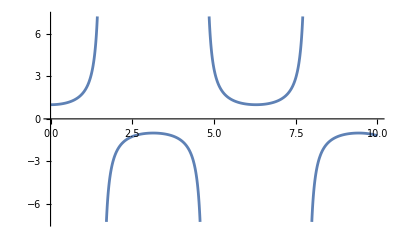

```mathematica
Plot[Sec[x],{x,0,10}]
```

I don’t know how to get the PostScript representation of that image.

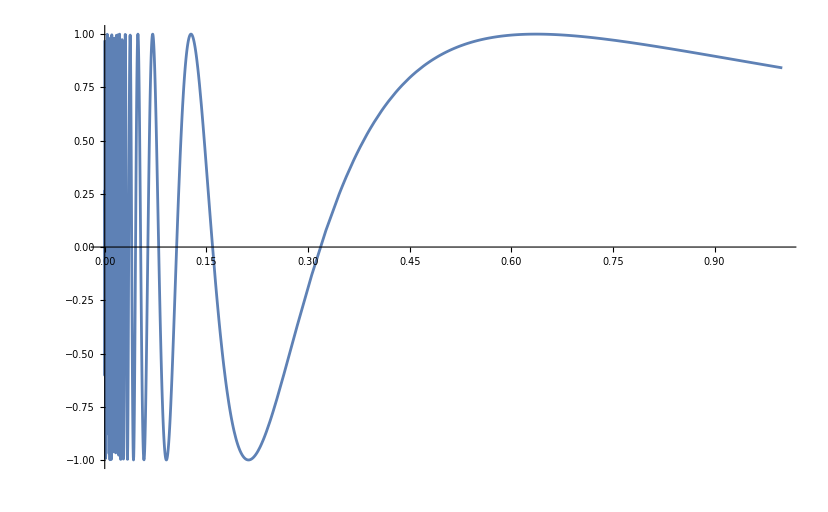

```mathematica
Plot[Sin[1/x],{x,0,1}]
```

```mathematica
??Plot
```

It’s different now, there is no “True” any more. So this is one example of what you can do here:

```mathematica
Plot3D[Im[Sec[x+I y]],{x,-3,3},{y,-3,3},Lighting->{{"Directional", Yellow, {0, 0, 3}}}]
```

-Graphics3D-

```mathematica
Plot3D[Im[Sec[x+I y]],{x,-3,3},{y,-3,3},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Show[,ViewPoint->{4, 5, -7}]
```

-Graphics3D-

```mathematica
Show[,ViewPoint->{4, 5, -7}]
```

-Graphics3D-

I don’t have the file “Polyhedra.m”, but we can still look at the Dodecahedron in 3D.

```mathematica
Graphics3D[Dodecahedron[]]
```

-Graphics3D-

```mathematica
Needs["PolyhedronOperations`"]

Stellate[PolyhedronData["Dodecahedron"]]
```

-Graphics3D-

This Tetrahedron is glued into each of the faces of the Dodecahedron. The result of this is above.

```mathematica
Graphics3D[Tetrahedron[]]
```

-Graphics3D-

Again, I don’t know how to draw inside the plot and then take the points out as data.

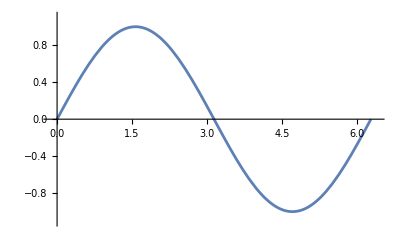

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

But I can create a set of data that’s similar to one that I would draw as an approximation to the sin curve above.

First an example of how to get data for the {x, y} points of Sin in the range [0, 2 Pi] in steps of 0.1

{{0.,0.},{0.1,0.0998334},{0.2,0.198669},{0.3,0.29552},{0.4,0.389418},{0.5,0.479426},{0.6,0.564642},{0.7,0.644218},{0.8,0.717356},{0.9,0.783327},{1.,0.841471},{1.1,0.891207},{1.2,0.932039},{1.3,0.963558},{1.4,0.98545},{1.5,0.997495},{1.6,0.999574},{1.7,0.991665},{1.8,0.973848},{1.9,0.9463},{2.,0.909297},{2.1,0.863209},{2.2,0.808496},{2.3,0.745705},{2.4,0.675463},{2.5,0.598472},{2.6,0.515501},{2.7,0.42738},{2.8,0.334988},{2.9,0.239249},{3.,0.14112},{3.1,0.0415807},{3.2,-0.0583741},{3.3,-0.157746},{3.4,-0.255541},{3.5,-0.350783},{3.6,-0.44252},{3.7,-0.529836},{3.8,-0.611858},{3.9,-0.687766},{4.,-0.756802},{4.1,-0.818277},{4.2,-0.871576},{4.3,-0.916166},{4.4,-0.951602},{4.5,-0.97753},{4.6,-0.993691},{4.7,-0.999923},{4.8,-0.996165},{4.9,-0.982453},{5.,-0.958924},{5.1,-0.925815},{5.2,-0.883455},{5.3,-0.832267},{5.4,-0.772764},{5.5,-0.70554},{5.6,-0.631267},{5.7,-0.550686},{5.8,-0.464602},{5.9,-0.373877},{6.,-0.279415},{6.1,-0.182163},{6.2,-0.0830894}}

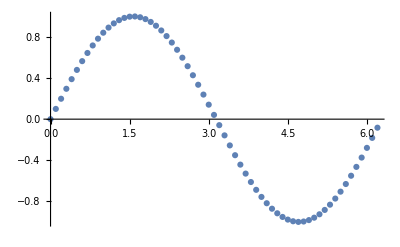

```mathematica
sinData=Table[{x,Sin[x]},{x,0,2 Pi,0.1}]

ListPlot@sinData
```

Now we can add some noise to the date. This way we simulate our approximation data.

```mathematica
RandomReal[0.1]
```

0.0986829

```mathematica
RandomChoice[{-1,1}]
```

1

This fGetSomeNoise function adds noise to the sin value.

{{0.132307,0.132307},{0.00584909,0.0056825},{0.131554,0.130223},{0.356141,0.351661},{0.440239,0.429658},{0.417879,0.397305},{0.509925,0.474568},{0.837887,0.782105},{0.892306,0.809662},{0.814485,0.697811},{1.05319,0.89466},{1.1837,0.974903},{1.11729,0.849333},{1.28742,0.950982},{1.51952,1.10497},{1.42272,0.920217},{1.73718,1.13676},{1.71523,1.0069},{1.82997,1.00382},{2.02326,1.06956},{1.94732,0.856613},{1.9534,0.716612},{2.14949,0.757984},{2.21858,0.664282},{2.50876,0.784221},{2.46934,0.567812},{2.46437,0.379874},{2.76567,0.493049},{2.68627,0.221263},{2.83977,0.179021},{2.92603,0.0671527},{3.03513,-0.0232921},{3.14014,-0.118231},{3.28956,-0.168183},{3.40911,-0.246426},{3.50302,-0.347765},{3.64658,-0.395939},{3.66883,-0.561005},{3.67471,-0.737145},{4.00073,-0.587036},{4.01204,-0.744763},{4.18219,-0.736088},{4.30796,-0.763618},{4.37947,-0.836695},{4.33442,-1.01718},{4.42638,-1.05115},{4.73701,-0.856683},{4.8296,-0.870323},{4.83999,-0.956172},{4.86639,-1.01606},{4.9612,-0.997722},{4.96224,-1.06358},{5.25786,-0.825598},{5.41078,-0.721485},{5.44098,-0.731784},{5.59137,-0.614168},{5.63774,-0.593527},{5.66354,-0.587148},{5.78671,-0.477893},{5.98238,-0.291501},{5.90934,-0.370075},{6.04742,-0.234743},{6.31673,0.0336453}}

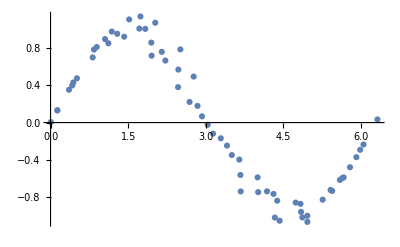

```mathematica
fGetSomeNoise[]:=RandomChoice[{-1,1}] × RandomReal[0.15]

sinApproximation=Table[{x,Sin[x]} + fGetSomeNoise[],{x,0,2 Pi,0.1}]

ListPlot@sinApproximation
```

Now we create a fit function to our sinApproximation data and plot the approximate points together with the fit function.

0.0200547+1.27741 x-0.473542 x^2+0.00704726 x^4

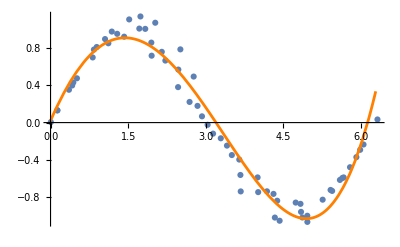

```mathematica
sinApproxFit=Fit[sinApproximation,{1,x,x^2,x^4},x]

Show[
ListPlot[sinApproximation],
Plot[sinApproxFit,{x,0,2 Pi},PlotStyle->Orange]]
```

## Programming (39:56)

```mathematica
fac[1]=1
```

1

```mathematica
fac[1]
```

1

```mathematica
fac[12]
```

fac[12]

```mathematica
fac[n_]:=n fac[n-1]
```

```mathematica
fac[20]
```

2432902008176640000

```mathematica
fac[20] == 20!
```

True

```mathematica
?fac
```

```mathematica
log[a b^2 c^3 d^4 e^5]
```

log[a b^2 c^3 d^4 e^5]

```mathematica
log[x_ y_]:=log[x] + log[y]
```

```mathematica
log[a b^2 c^3 d^4 e^5]
```

log[a]+log[b^2]+log[c^3]+log[d^4]+log[e^5]

```mathematica
log[x_^n_]:=n log[x]
```

```mathematica
log[a b^2 c^3 d^4 e^5]
```

log[a]+2 log[b]+3 log[c]+4 log[d]+5 log[e]

```mathematica
??log
```

```mathematica
g/:g[x_] + g[y_]:=g[x+y]
```

```mathematica
?g
```

```mathematica
g[a]+g[b]+g[c]+g[d]
```

g[a+b+c+d]

```mathematica
Expand[(x+y)^3/z]
```

x^3/z+(3 x^2 y)/z+(3 x y^2)/z+y^3/z

```mathematica
TeXForm@
```

\frac{x^3}{z}+\frac{3 x^2 y}{z}+\frac{3 x y^2}{z}+\frac{y^3}{z}

```mathematica
FortranForm@
```

x**3/z + (3*x**2*y)/z + (3*x*y**2)/z + y**3/z

```mathematica
CForm@
```

Power(x,3)/z + (3*Power(x,2)*y)/z + (3*x*Power(y,2))/z + Power(y,3)/z

This is how you look for other built-in functions that end with “Form”:

```mathematica
Names["*Form"]
```

{AccountingForm,AnatomyForm,BaseForm,BlankForm,BoxForm,CapForm,CForm,ColonForm,ColumnForm,DecimalForm,DisplayForm,EdgeCapForm,EdgeForm,EdgeJoinForm,EngineeringForm,ExportForm,FaceForm,FillForm,FontForm,FortranForm,FullForm,HoldForm,HorizontalForm,HornerForm,InputForm,JoinForm,LongForm,MathMLForm,MatrixForm,NumberForm,OutputForm,PaddedForm,ParentForm,PercentForm,PolynomialForm,PrecedenceForm,PrintForm,PromptForm,QuantityForm,RealBlockDiagonalForm,RecurringDigitsForm,ResponseForm,RuleForm,ScientificForm,ScriptForm,SequenceForm,ShowShortBoxForm,SpaceForm,StandardForm,StringForm,StrokeForm,StyleForm,SurdForm,SyntaxForm,TableForm,TeXForm,TextForm,TraditionalForm,TreeForm,ValueForm,VerticalForm}